```mathematica
SetOptions[$FrontEnd,Magnification->1.05]
```

## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
```

## Compare with other Brito el al. data

```mathematica
ZBCP=GroupBy[{N@Round[#1,10^-5.],#2(1+Sqrt[1-#1^2]),#3}&@@@Import@GetZFileBCP[-1,1,1],First->(Drop[#,1]&)];
Z=GroupBy[{N@Round[#1,10^-5.],#2,#3,#4,#5}&@@@Import@GetZFile[1,1,1],First->(Drop[#,1]&)];
Zp=GroupBy[{N@Round[#1,10^-5.],#2,#3,#4,#5}&@@@Import@GetZFile[1,1,1,"precision_p12_a15_auto"],First->(Drop[#,1]&)];
Z2=GroupBy[{N@Round[#1,10^-5.],#2,#3,#4,#5}&@@@Import@GetZFile[1,1,1,"test1"],First->(Drop[#,1]&)];
```

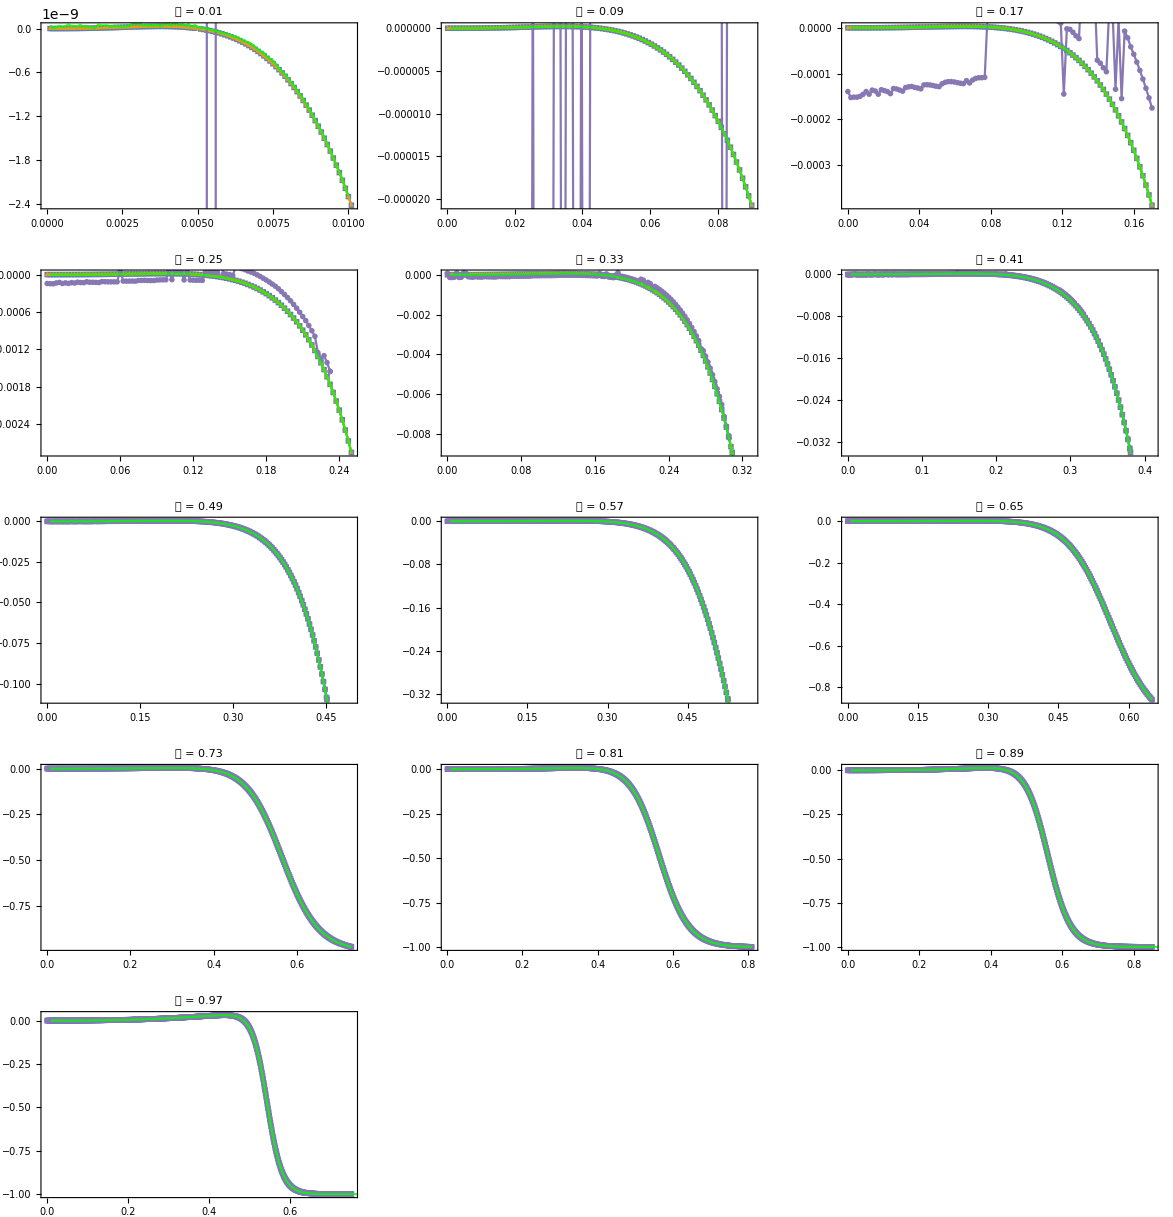

```mathematica
Show[
ListPlot[Z[#][[All,{1,2}]],Joined->True,PlotStyle->ColorData[97,1],PlotMarkers->{■,Small}],
ListPlot[Z[#][[All,{1,3}]],Joined->True,PlotStyle->ColorData[97,2],PlotMarkers->{▲,Small}],
ListPlot[Z[#][[All,{1,4}]],Joined->True,PlotStyle->ColorData[97,5],PlotMarkers->{●,Small}],
ListPlot[ZBCP[#],Joined->True,PlotStyle->{Opacity[0.8],Green}],
ImageSize->Medium,PlotLabel->StringRiffle[{"𝒥","=",#}," "],Frame->True
]&/@Take[sameJ,{1,Length@sameJ,8}]//GraphicsGrid@Partition[#,3,3,1,{}]&
```

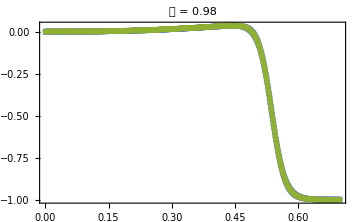
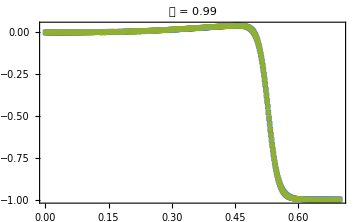
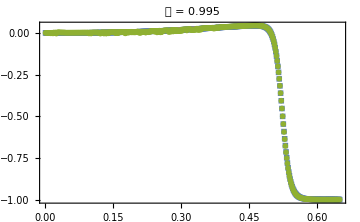
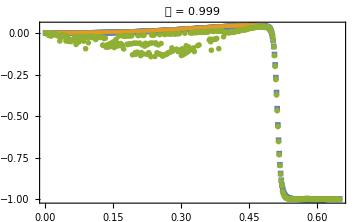
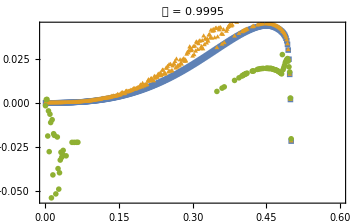
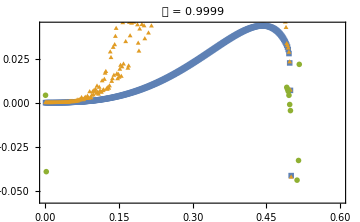

```mathematica
Show[
ListPlot[Z[#][[All,{1,2}]],Joined->False,PlotStyle->ColorData[97,1],PlotMarkers->{■,Small}],
ListPlot[Z[#][[All,{1,3}]],Joined->False,PlotStyle->ColorData[97,2],PlotMarkers->{▲,Small}],
ListPlot[Z[#][[All,{1,4}]],Joined->False,PlotStyle->ColorData[97,3],PlotMarkers->{●,Small}],
ImageSize->Medium,PlotLabel->StringRiffle[{"𝒥","=",#}," "],Frame->True
]&/@Keys[Z][[-6;;]]
```